```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

## -1/3 < m < 0

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

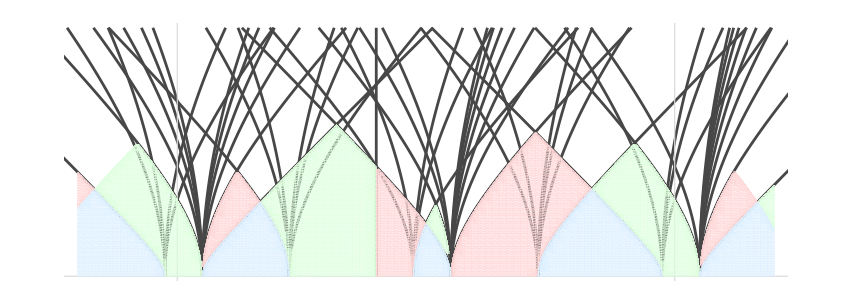

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=-1/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

plt1=Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

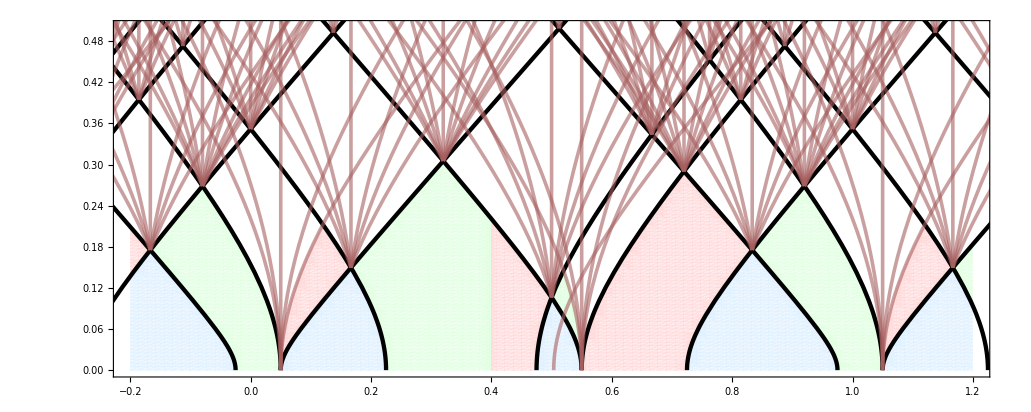

```mathematica
Show[domainI,domainII,domainBr,temp,AspectRatio->Automatic]
```

## 0 < m < 1/3

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

{{1,0},{2,1},{3,2},{4,2},{5,3}}

{{0,0},{1,1},{2,2},{3,2},{4,3}}

{{0,0},{1,1},{2,2},{3,2},{4,3}}

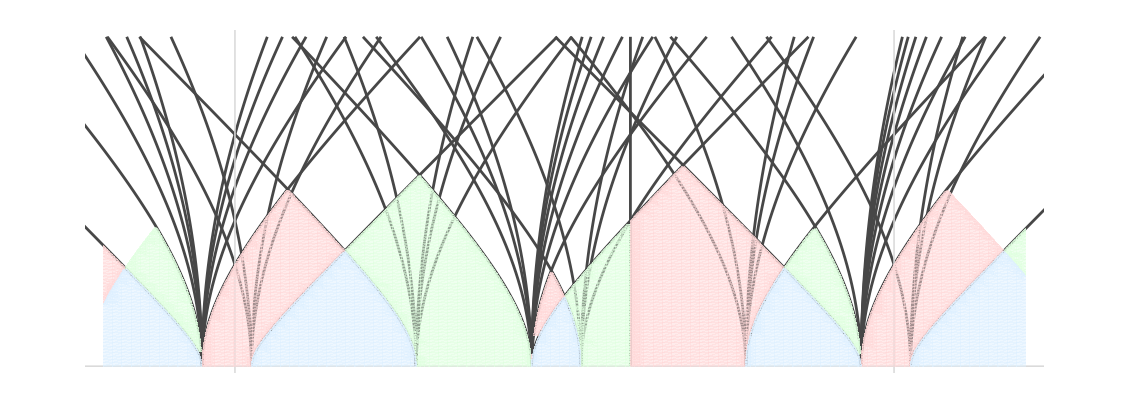

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=1/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Echo@ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

## 1/3 < m < 2/3

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

{{1,1},{2,1},{3,2},{4,3},{5,3}}

{{0,1},{1,1},{2,2},{3,3},{4,3}}

{{0,1},{1,1},{2,2},{3,3},{4,3}}

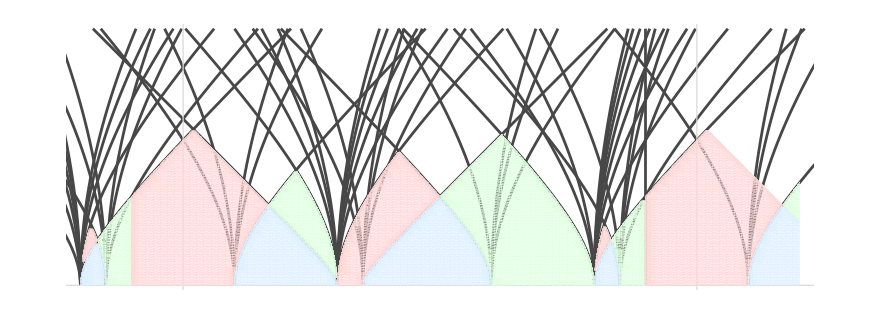

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=4/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Echo@ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

```mathematica
SpectralFlow[GV[0,-1,-1/2]/.repCh,{-3,-2}]
```

{0,0,-1,1/2}

```mathematica
Ch[0,0]-Ch[0,1]/.repCh
```

{0,0,-1,1/2}

```mathematica
With[{m=2/5},Flatten@Table[k+{m/4, (m+1)/4, (1-m)/2, (m+2)/4, m+1/2, (m+3)/4, 1-m/2}, {k,0,0}]]
```

{1/10,7/20,3/10,3/5,9/10,17/20,4/5}

```mathematica
{m/4, (m+1)/4, (1-m)/2, (m+2)/4, m+1/2, (m+3)/4, 1-m/2}
SortBy[%, #/.{m->2/5}&]
```

{m/4,(1+m)/4,(1-m)/2,(2+m)/4,1/2+m,(3+m)/4,1-m/2}

{m/4,(1-m)/2,(1+m)/4,(2+m)/4,1-m/2,(3+m)/4,1/2+m}

```mathematica
DSZ[Ch[1,1],-Ch[0,1]]/.repCh
```

2

```mathematica
DSZ[Ch[2,1],-Ch[0,1]]/.repCh
```

4

```mathematica
ChernToCh[2Ch[1,1]-Ch[0,1]/.repCh]
```

Ch[2,1]

```mathematica
DSZ[Ch[1,1],-Ch[2,2]]/.repCh
```

-3

```mathematica
DSZ[Ch[3,2],-Ch[2,2]]/.repCh
```

2

```mathematica
(x^10-8*w*x^9+288*w^2*x^8+768*w^3*x^7+9552*w^4*x^6+399744*w^5*x^5+89472*w^6*x^4+17799168*w^7*x^3-10849280/2187*x^2-164749312/19683*w*x-89989120/19683*w^2)/.{w->u}
%-((10 u+x) (208 u^3+120 u^2 x-6 u x^2+x^3)^3)//Expand
```

-(89989120 u^2)/19683-(164749312 u x)/19683-(10849280 x^2)/2187+17799168 u^7 x^3+89472 u^6 x^4+399744 u^5 x^5+9552 u^4 x^6+768 u^3 x^7+288 u^2 x^8-8 u x^9+x^10

-(89989120 u^2)/19683-89989120 u^10-(164749312 u x)/19683-164749312 u^9 x-(10849280 x^2)/2187-97643520 u^8 x^2

```mathematica
((x+10*u)*(x^3-6*u*x^2+120*u^2*x+208*u^3)^3)/((x^2-8*u*x+144*u^2))/.{u->w,x->JG}
```

((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)

```mathematica
((x+10*u)*(x^3-6*u*x^2+120*u^2*x+208*u^3)^3)/((x^2-8*u*x+144*u^2))-((x^10-8*w*x^9+288*w^2*x^8+768*w^3*x^7+9552*w^4*x^6+399744*w^5*x^5+89472*w^6*x^4+17799168*w^7*x^3-10849280/2187*x^2-164749312/19683*w*x-89989120/19683*w^2)/(x^2-8*w*x+144*w^2))/.{w->u}
Simplify[%]
```

((10 u+x) (208 u^3+120 u^2 x-6 u x^2+x^3)^3)/(144 u^2-8 u x+x^2)-(-(89989120 u^2)/19683-(164749312 u x)/19683-(10849280 x^2)/2187+17799168 u^7 x^3+89472 u^6 x^4+399744 u^5 x^5+9552 u^4 x^6+768 u^3 x^7+288 u^2 x^8-8 u x^9+x^10)/(144 u^2-8 u x+x^2)

(13312 (1+19683 u^8) (6760 u^2+12376 u x+7335 x^2))/(19683 (144 u^2-8 u x+x^2))

```mathematica
((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)
```

```mathematica
MirrorCurveJ[m,u]
```

((1-8 m u^2-24 u^3+16 m^2 u^4)^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4))

```mathematica
Discriminant[Numerator@Together[((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)-j],JG]/.{w->-(-1/3^9)^(1/8)}//Simplify
```

8589934592/9 (-1/3)^(1/4) (-1728+j)^5 j^6

```mathematica
((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)/.{JG->(a[m] u+b[m])/(c[m] u + d[m])}//Together//Simplify
```

((u a[m]+b[m]+10 w (u c[m]+d[m])) (u^3 a[m]^3+b[m]^3-6 w b[m]^2 (u c[m]+d[m])+120 w^2 b[m] (u c[m]+d[m])^2+208 w^3 (u c[m]+d[m])^3+3 u^2 a[m]^2 (b[m]-2 w (u c[m]+d[m]))+3 u a[m] (b[m]^2-4 w b[m] (u c[m]+d[m])+40 w^2 (u c[m]+d[m])^2))^3)/((u c[m]+d[m])^8 (u^2 a[m]^2+b[m]^2-8 w b[m] (u c[m]+d[m])+144 w^2 (u c[m]+d[m])^2+2 u a[m] (b[m]-4 w (u c[m]+d[m]))))

```mathematica
Simplify@Series[((1-8 m u^2-24 u^3+16 m^2 u^4)^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4)), {u,0,1}]
```

1/(m u^8)-1/(m^2 u^7)+(-16+1/m^3)/u^6-(1+28 m^3)/(m^4 u^5)+(1/m^5+27/m^2+96 m)/u^4+(272-1/m^6-26/m^3)/u^3+(1+25 m^3+216 m^6-256 m^9)/(m^7 u^2)-(1+24 m^3+192 m^6+576 m^9)/(m^8 u)+(432+1/m^9+23/m^6+169/m^3+256 m^3)-((1+22 m^3+147 m^6+256 m^9) u)/m^10+O[u]^2

```mathematica
Solve[{
((a+10 c w) (a^3-6 a^2 c w+120 a c^2 w^2+208 c^3 w^3)^3)/(c^8 (a^2-8 a c w+144 c^2 w^2))==(4096 m^6)/(-27+16 m^3),

}]
```

```mathematica
Series[(u^2 a[m]^2+b[m]^2-8 w b[m] (u c[m]+d[m])+144 w^2 (u c[m]+d[m])^2+2 u a[m] (b[m]-4 w (u c[m]+d[m]))), {u,0,100}]
```

(b[m]^2-8 w b[m] d[m]+144 w^2 d[m]^2)+(-8 w b[m] c[m]+288 w^2 c[m] d[m]+2 a[m] (b[m]-4 w d[m])) u+(a[m]^2-8 w a[m] c[m]+144 w^2 c[m]^2) u^2+O[u]^101

```mathematica
w0=-(-1/3^9)^(1/8);
```

```mathematica
((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)
```

((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)

```mathematica
Haupt272=q8^-1-18*w^2*q8-240*w^3*q8^2+288*w^4*q8^3-2304*w^5*q8^4-10176*w^6*q8^5+31680*w^7*q8^6-111987*w^8*q8^7+243712*w^9*q8^8+712170*w^10*q8^9+19958112*w^11*q8^10-28207584*w^12*q8^11+276046848*w^13*q8^12+887569344*w^14*q8^13-2305816704*w^15*q8^14+7054569063*w^16*q8^15-14852800512*w^17*q8^16-80275282596*w^18*q8^17-1523315678256*w^19*q8^18+1795538668320*w^20*q8^19-17645886549504*w^21*q8^20-59612160068352*w^22*q8^21+150606169190208*w^23*q8^22-449633754879408*w^24*q8^23+987768025030656*w^25*q8^24+3744478650972366*w^26*q8^25+85308983685181920*w^27*q8^26-109133967809741760*w^28*q8^27+991792005122598912*w^29*q8^28+3191924989212280512*w^30*q8^29-8215329366207897984*w^31*q8^30+24639316155653301009*w^32*q8^31-50317494582870933504*w^33*q8^32-221502407257449884520*w^34*q8^33-4425249769979601636576*w^35*q8^34+5331508577832015189504*w^36*q8^35-49411801117741809966336*w^37*q8^36-160047645434924554689984*w^38*q8^37+399784297622274491822784*w^39*q8^38-1163502239121306423100080*w^40*q8^39+2447488377844339949899776*w^41*q8^40+9785228983580052235217340*w^42*q8^41+205952062811404353097959936*w^43*q8^42-250818317288390414840493024*w^44*q8^43+2278205909680390934127971328*w^45*q8^44+7236259365382139335580445888*w^46*q8^45-17985199678768956492170877312*w^47*q8^46+52516553619483381707815999239*w^48*q8^47-107056796726759397244867510272*w^49*q8^48-449940702624670414732699993554*w^50*q8^49-9065871403057340283111534398736*w^51*q8^50+10838379421244693060413335738432*w^52*q8^51-98123445149873576547225070536192*w^53*q8^52-311456659184251129083742731296448*w^54*q8^53+768991663800614357960841208298880*w^55*q8^54-2218815238577926809497804866805157*w^56*q8^55+4552285844847044188460781882458112*w^57*q8^56+18324519475239735460391784681931032*w^58*q8^57+375137813580582396261825330088854240*w^59*q8^58-449546992048495843249358387708487648*w^60*q8^59+4037726457685624836671688901387106304*w^61*q8^60+12693390638887775133154864787039103168*w^62*q8^61-31182632556438262641346534403515654656*w^63*q8^62+89745928975578626930571836559168438162*w^64*q8^63-181891671587270831657587035025437622272*w^65*q8^64-745521295826296615960424079603340467552*w^66*q8^65-14959990913084806494490890345696594790656*w^67*q8^66+17724385385983786202964906457556449562400*w^68*q8^67-158836380475874596469468502656704906904064*w^69*q8^68-498421253837539225632456379401435237447936*w^70*q8^69+1217765117876979399779904806558529595747584*w^71*q8^70-3484049166761094769733291162444958107708499*w^72*q8^71+7060944090452552096110088894910579920246784*w^73*q8^72+28369156047166504888603487508643037932871484*w^74*q8^73+573017902540690678261117503628611214863840096*w^75*q8^74-679363992654990990332337775846774676473101792*w^76*q8^75+6048013844146298228932028890304489321749902336*w^77*q8^76+18865346977198273327934876580670341241193821440*w^78*q8^77-45957860388405684128101218176405250249740807040*w^79*q8^78+131116447236032973880489823566669263257966675982*w^80*q8^79-263834351518436094044778688403679025640423849984*w^81*q8^80-1067779082546631727158619912376628533820599434170*w^82*q8^81-21328436184472118307214758757039184452353854912352*w^83*q8^82+25119145643148584169153869191477767906596978580768*w^84*q8^83-223221683125401556977069211591572821299787790655488*w^85*q8^84-694851911074270822858929256952947770775181145525120*w^86*q8^85+1685742167615449798867508899019261760009828162325824*w^87*q8^86-4788035481755398380459495518631763171876566860529237*w^88*q8^87+9629587588698328499119110980378677867805086553530368*w^89*q8^88+38548051479278924164829031434775544279551717944964540*w^90*q8^89+771493059842879731105009402544076656420481648039822816*w^91*q8^90-907452643177005863836483856263629286806241817318229504*w^92*q8^91+8031925965855080740131553469720622603846175588319852544*w^93*q8^92+24902183554516275302786038940305022857246245536901780480*w^94*q8^93-60254149321789991854272725373483942229085229948537004800*w^95*q8^94+170798307509011858258260237936515250109183710002701850130*w^96*q8^95-341822721168099056854856176278480530108001925554513641472*w^97*q8^96-1372064069591979284178261483963936026300870759199843447204*w^98*q8^97-27284138679969666901404236930140631098733963459644641194352*w^99*q8^98+31961887822219661201613700719552506758882350123637068600672*w^100*q8^99-282274869865009550635365750851943633539944941407582458101504*w^101*q8^100-873414460972609076877296228457134278102355703201543932635584*w^102*q8^101+2107489678259491817286237122872908000594001907483946730541952*w^103*q8^102-5954902370483808270508993894726840723401619055182992164164611*w^104*q8^103+11903017975087236828699713402493691870445844995468786035544064*w^105*q8^104+47463495137078001559785808551819086303239273727763472530232704*w^106*q8^105+943913382487648551852666611622039042268073352681027384405802080*w^107*q8^106-1104161130563419212245268953693470826471029762963992040668306912*w^108*q8^107+9723912159985629920592972777551852627285947640899801042412218368*w^109*q8^108+30000147130761086031711141283422166547217054669069713101025386944*w^110*q8^109-72224202974647312499940306588999704485470475743433700501239057536*w^111*q8^110+203663591546485686057026911400843462642771815788562396062963164421*w^112*q8^111-405781223390652888432739995600189369068303592712514310407808221184*w^113*q8^112-1619190905523610007537216031581618059180280745975393717313250389284*w^114*q8^113-32067087398140960118118189307870144173617277568832707641046712454912*w^115*q8^114+37397095240023110389211655440937303090876143949689073112366225445376*w^116*q8^115-328731935708442180125483638281189321014200289299930216384668589635072*w^117*q8^116-1012382899479488146745603440938088568871860887827523501542729251285184*w^118*q8^117+2431713633062330742043238500374812245918802133132283882432858229445696*w^119*q8^118-6841094647744037100345019032637318645188671325845779115946418985046549*w^120*q8^119+13611066230866915891422732133031809684423444749589529179126778572357632*w^121*q8^120+54080118619441528826952675680394280281415753179613171966908486328184490*w^122*q8^121+1070408286605382550114858796984311645303809538119689487943815386345688288*w^123*q8^122-1246583014464015959264498987115199651221082034736465873676461259030283712*w^124*q8^123+10932627500495805083762431234518005807600818087238591144620945329225965568*w^125*q8^124+33592938465628409659148038273139307372597969697915419658622577286959121536*w^126*q8^125-80543105590878883222960636774680546924349074189038627471858950293956523648*w^127*q8^126+226200993174982064398909789524257275563260303783629499854624859657840212356*w^128*q8^127-448946048115453697188765849929612487982238415844965975918967056859523973120*w^129*q8^128-1783371950194094949462508003183723749325250994663702378736963057529273760360*w^130*q8^129-35193083531306240026037804854898122604300109971849614605654891359982233446080*w^131*q8^130+40891057167688834382046714893043799058663953194460575546531141793847499803424*w^132*q8^131-358051426894876934709561915139393463987278326099200386691113197160111083859968*w^133*q8^132-1098447756478554943777646370218500428769747362701446660791496306417717996063488*w^134*q8^133+2628702933527387719504155228148272354640368683114858269023769474290686870259648*w^135*q8^134-7368230407844883329593510835581628293143516168073759042912394207666013010529382*w^136*q8^135+14604807225824552421681854494581974137651796384752096592080552709652496157503488*w^137*q8^136+57842770497807691072376669022957979201395698491826407715869981380389300459322300*w^138*q8^137+1140474055284780139460711183730743198293654120457447553863183167363154704379911680*w^139*q8^138-1323321357017056679274661034700794753550818728734263971079192879640520515216235488*w^140*q8^139+11566087101576991433128084558164994536130531765620630553109194663987203769934524416*w^141*q8^140+35418538188722538891267856244581038357534764995427689463309066023189841898607449600*w^142*q8^141-84626397650890759747843997233732013739049358591698953178981070750052221361818770560*w^143*q8^142+236854153748182306964749502747671974891477161843208967329070049638836349438589469603*w^144*q8^143-468567906803055348410229052808731245059721208598310202608449289274818281945817071616*w^145*q8^144-1854612946602233503425427531484357282742117839658922332375212569655899166833795199712*w^146*q8^145-36486734339836892303130740171999241274420521661337207813705122138506496232131526844768*w^147*q8^146+42260393440768820889397566101583516936623051240289214082309059954294213354259462318880*w^148*q8^147-368831860110094957123939036681866973001399746069958474877507122120003222815310344293888*w^149*q8^148-1127878577248093642758202150798457416004974910246864749645038357651272507388354497704128*w^150*q8^149+2690707972509338811957387771381297138887154321868995009689528666796732234802045162477632*w^151*q8^150-7518825640824952158333490344954464294510408034030536931786768685644281728281824375710650*w^152*q8^151+14855992937491609643348926490235877842153616618210284716542655103209645787982468468776960*w^153*q8^152+58670752817551236953391350173809451224935469771106551171836525145868019299564619897906004*w^154*q8^153+1153130171008551830463826355290449547453485066079470595230214762041181086797940384666607104*w^155*q8^154-1333930459972931166748017737501263574622958562209242672356060810216534806870668475043506176*w^156*q8^155+11624486179184700383970208414278802854156474671998015255776818190187560696833872025282844672*w^157*q8^156+35493704974139407300414630317912512125885871904703901895422250336992553224394392510441052864*w^158*q8^157-84558534775706601668043283933521878813585010211883476058174141871760065545385067605334590720*w^159*q8^158+235975228393517074140651320875846516174945229402310872302247557823677858947461909112789220677*w^160*q8^159-465523710440007891605134549943354015263130171802371164374214773142312445067540764063404130304*w^161*q8^160-1837039767562525064824433384424770044941398527273125177031170947392372885732677198213164728704*w^162*q8^161-36043291268757759955067169612931807205449987664750301006779387796894598598696939251429929238896*w^163*q8^162+41632126891059830849506856596578776166209108178944864364065073966020699200655955478128471567648*w^164*q8^163-362344738236362676182807644333085593643490990117186095979892162147730660313002581368130739341824*w^165*q8^164-1104994267131732494402020846950114531983148626612105412514129573934289978390690554272205053591296*w^166*q8^165+2628981690060221967176977046644026432345992611773179585728581224238450383860076211189888648175296*w^167*q8^166-7326765908181840870076006996789951082432426236638880963151564575411336299681684019566811424955126*w^168*q8^167+14437479931130307339428584947362941275699373153852013838826778168450744832574045058851856548823040*w^169*q8^168+56874880299835712599820886095532574118033832646427470151304486854964214436862090712432260075127950*w^170*q8^169+1114829332070380075176982455454858428238408178783537627856903237854647635343635145187552782305915072*w^171*q8^170-1286246418070830025243358044659033058094155418547913508467210191996867275023572292367991993651517344*w^172*q8^171+11180282425915144788103431677241823914334740765126265437124315639989894829353634997758132038899248128*w^173*q8^172+34051106026141039076644240293452347411827939811261771796196317107913054363100354339745195495363512768*w^174*q8^173-80917015023888175642678437352099085355056779085250106182629605198747897609111438141345451562307174272*w^175*q8^174+225246316344857302861352192049779923784023282198716772590757176730596184040332873391440508106685297626*w^176*q8^175-443268008087413205374532629402068618692763302360445886649279886154026244043831570976065333855784468480*w^177*q8^176-1744745850091271334445934139896341346080166014949247975257913761960450407321178746928776934012805303528*w^178*q8^177-34151168941047324201946865722494800831975215745726712305901146270990932976306663909956414152393956026464*w^179*q8^178+39352405646258675558853833852988076909268279252269827348123955569672355862930136986646446595110956081440*w^180*q8^179-341677706267623948130001997431755590703191351888201988028451840292937891233222486845114050215122891310592*w^181*q8^180-1039477907002476300674390638029629177077737862979370326374302829657437699802555863905484572745787095599808*w^182*q8^181+2467287107766372873555420042818112284738467725559323336820574796771281004670793978313339955224327577991424*w^183*q8^182-6860085742905068669436656446107339008533000242058730245748959863146642078436539239015957178325735717331887*w^184*q8^183+13486237516378018929892678011907208757836888845410217718575638562981955908574445443537859428239662181957632*w^185*q8^184+53009226981730706070203046977429737063745896859233714172717304019079784456541103693828857158432850173324384*w^186*q8^185+1036631039079150208394959227114244512452574936906038327143955362531754662439686692294434150161201385479907328*w^187*q8^186-1193287197614783658839033134284699616824401212396518830734522182347916091604704731852862571709460078343110080*w^188*q8^187+10349090835316716334081016700579581057784783751206135652893981762402325111967821791254033375905611906950000640*w^189*q8^188+31449629045739822415423163494311373256074126197718602513848284219669148861363380627287358336178385555516787200*w^190*q8^189-74569230034742556996375026650320126520742778545012780166681641655236981754111943583181189384024972607299934080*w^191*q8^190+207119259417193464184487321455791042061780168170482616876679181332597396387575717556174532756672784838481484552*w^192*q8^191-406715203283619891661926536201542609729862922053631102851529357743858593938789774536730652903017311007387156480*w^193*q8^192-1597319243441347517791746333668249190661709506314760885292971785998535136251331670791038452920428568960599735972*w^194*q8^193-31199655153837754868542474215290964504490429047112696281008502075162696472860356930417236975764860113928288473056*w^195*q8^194+35875427398794206668620967802643645063181807151293980400161161895002695035702854833728867339197069590839615054336*w^196*q8^195-310827909681517753946551394346187469922888771150842866001878374512569976639948963715785061778920364136480681013504*w^197*q8^196-943634824200339528171521248266351170499462349908262486765678620869071631643941697819287675170674323474638717852608*w^198*q8^197+2235145132255926855644221481120896110373917825672063608883566297171060117399635335041089213528008306279543464528448*w^199*q8^198-6201848810458508079684775514800218571896706551647551773027813794533334463745932147679676339774422459383960087590172*w^200*q8^199+12167011202491303430153115962536609304314171148533911195025258995621056501654609757030117779360824225911761107519488*w^201*q8^200+47728679120864416423365366795352580521785750960013227320417818149636778380126308692634277182660085376662801936300696*w^202*q8^201+931453732693546767581967364264778640217083827585415319540097875572442997890398166036819042776386937933245176705091424*w^203*q8^202-1070054517019676460890458928024113220953650597960898260002100100282897262716199635516709345202484086135791920343490048*w^204*q8^203+9261900738973263310300015392072796700208812862270594816390657855188651896925679617708238477145220499885755853222512640*w^205*q8^204+28090341873156170317882622610047469026333199348598512680035428108137115513550741536882630628832550341913101698171663488*w^206*q8^205-66473370634762397613245028410594536515685251394202108603394486595514091082123173291584957570534820130194811188875058816*w^207*q8^206+184271929649370852466416215219863702064136339335939982772596958991302835746573443988069282272498816249202740784798843263*w^208*q8^207-361155467874272011716257350479796621557372360964342695444766907024899360147900375186790495032743501303758255629785268224*w^209*q8^208-1415616661315395321055139673087056786983301263667876654057507867946621415133744673609970089313203132778507944514544055528*w^210*q8^209-27598456492062001836182730108548831200490185680133941206838477837477820324456552978612855000282678906543391604098637407232*w^211*q8^210+31674718554901948638580988666140594809407139455296472300727382858021666290107164390599963041577978579828644924053313046816*w^212*q8^211-273915999374301260832997017861728813935255603135582583959620703892081241738137572775584160348186322361547739438213592727040*w^213*q8^212-830018934996832014241595842162409816541046114418638182601114559238311947414785904658686466444252460212628647946369887834880*w^214*q8^213+1962384538381904714626825625350042324109287124723088975141429361472055714515575557907283318645062324221858407806986888018240*w^215*q8^214-5435016308022572937724532083331330155796991962515011854512710189318850484404665190571796036017348322290643086614269539629668*w^216*q8^215+10643025853756706596979575313912250194644420325140327030832660777096072096709255390906408569075220741221670478354914503049216*w^217*q8^216+41675749532099135930393761565791772028244533650884508076342151478202953799637828230142192100748460640306014485344945447843328*w^218*q8^217+811846411148672192323093478220502715210701273216711408956615689609229039969003931786714743607763939723819361145433467328319456*w^219*q8^218-930972375942108102496035169787128227932688225510577500606872905197909841047902090351927163754387736337944803452895551169954752*w^220*q8^219+8043753491189182308575933828007437155461405779851936416595320616085969000148966818073408323627141707859100581014742435396806656*w^221*q8^220+24352809725315812989309120666925073525750611690027506570364452534626662228187192278069457220817333058512461992771627530035073920*w^222*q8^221-57527635195010326883057124409910283852340169680831275092570718379960307151384283442355846194981126161110415436627087628729575808*w^223*q8^222+159194952098199194269765378383035743443306866631822355051804854860957272966688784122612346171399435540028770825115327912143497898*w^224*q8^223-311468495378666163731697130461454572888473366998399174686989856394608075087816007579235392569540265668204743403309506258059395072*w^225*q8^224-1218731831292926501423993809735555057236227065654530295157669479183128186214361726161222480051372260258866018282325893425877129910*w^226*q8^225-23719765519733724958071282942309019545232600759448426415194768387529812997347725737071071461831339869586999745356284307112707424992*w^227*q8^226+27177091555970528840516945878218729053969878482437813583495960779043923145398177990852257611789263785015542256381128232911458451744*w^228*q8^227-234624341333001166202932192717280403515771127782867376132490418224427017654704033760116651122512507982707531533863011154130252877824*w^229*q8^228-709763797011140517570570778778122140471384901021386218989691240826555050503538064960239908206264828167158552356802814148196116958656*w^230*q8^229+1675276970443231883526350385763838983908218557026814821636420156447323649152395133299338334877136091291850046144620668801522862466816*w^231*q8^230-4632173625002437055627166171842344725578239817182751412077022145108615592777063288033825755763252707084134859917461275424412958722444*w^232*q8^231+9055912245448809357444392384761237663543343498553408549870996720489652930661868550992870877528641384862276786338917420215188780994560*w^233*q8^232+35403642178427350801759546665044691957271389319715457306357512515863170478459051876683843273101102683738052069393726682714715128699196*w^234*q8^233+688537666589108835963067299989140719062319296410035007851120940982592758719135677288735868868594448926282122538889278724681074187033696*w^235*q8^234-788292195310409408775106537034906073333440122700325836808666851836891875876060243322847427110906008214133306851102340661858613572635648*w^236*q8^235+6800074638700648723575018082013793769144414663362831444291504236509896937994122817283101697187832527488261913917436016178959534353480704*w^237*q8^236+20554771291295725755571056369882220145432501477106113202829606331409874594832079831697075047576429961911627626918999511849487689090476544*w^238*q8^237-48478755562321160977854698651682402235484849267914085849968289351633095259617725181795854308950155671657701211810475911955422027681331456*w^239*q8^238+133942899432855381975801758554052972933457215312524393513659397591652141825052723539715002884499693259292591849848871366617442921036191732*w^240*q8^239-261653759423415194602389566211510284424124984402159301348128032919190188524167072011932744983505003024825253550917164550655064485250072576*w^241*q8^240-1022208941226322435911783871056490584005551809284521272238569426069290191325488471486537126393607682154173243304357385631526851691782230436*w^242*q8^241-19864371079251198648861699687721498734913854440014882634191888118353189317071205792184322581535494714782111794371178222385543925327806767280*w^243*q8^242+22724899570677539354303609702750070636231255034617409453840521038993053159544984095340998515732458828258061298424286413863324841534781050208*w^244*q8^243-195888091137713751322021844160147772819408667635601965348924626472169540752676371790600529721140436105785415399732803876174796458779464472064*w^245*q8^244-591682794908776872561183282864768503209115937480103992674972594488946971796370318551115912024698845166391432221233851006106341627555038156736*w^246*q8^245+1394463090919593436638535399458598841623118528560018817077295579998741789492744295161483891596002710642458624038095154514849669797442920408448*w^247*q8^246-3849947456591929100772078855172505310343055340496448039763736423427835639465047167501034249944483500104130284906294707558025980551522676467822*w^248*q8^247+7515418842160974321808643822449998431539872294772524070857709646332140079746624443372169059017194098936367865943500475296073764644812396494848*w^249*q8^248+29337988257055546690783065872371979130320328591443411516466209599512634831190347536164299816166274480648221250080588125285301685697504835439384*w^250*q8^249+569727659195634695949452888828546214605551004858627947395929743717919424234343192824981726663171968025640497719099809490811657782446935199132608*w^251*q8^250-651313094528205786224243119193444538277638436912116337902536935717531095124207705513572533712519951558618343401539300951716217076663628241285088*w^252*q8^251+5610282971951332033732570431154900162335587747364709083688931177991657733894102267030130803863465347306017581923800914891585298705982230833580032*w^253*q8^252+16933861547395476497082907230522159913109006581743372139782457855585146292432696029083802684544933258647263976500435451794470390621535396962354944*w^254*q8^253-39881357833391953601793837832140317738739928089020907385658222830620040214944372837732927967194745864549091320898196599913307402508267764774430720*w^255*q8^254+110031371307157523149939547834070240438838595885796368917572519228507674473575328305239190616711838548081913197540317695698350676978645178618005359*w^256*q8^255-214638538312873503301695874314381258990476914509355245289669951480099589825491602104413446147431163546564076845773092030503345831214420240870932480*w^257*q8^256-837341456555334737473057036213913572783571247539429251556489046015137698572860009731230854230296050870501645886845628912011918416853229039683435556*w^258*q8^257-16249119231312469759878598229738741036727721369012730517640336006841978052807021347192256060788287148345378789157870734458621367540980919999247835392*w^259*q8^258+18563121636632298505975217978119754203271902281748106602965555010992435152683097313523008954738259346529679917561537082232235313969197151384005576192*w^260*q8^259-159791364964923774220147408419850507161227750809156777519465296611073509656743019928228046157568013401239148865087923201144312552951392107932509271040*w^261*q8^260-481985205305936817854849792207520457563580747550838799986169690332162639630243870598155529592860291949972315651752351436822166211190148271189356292032*w^262*q8^261+1134371375680247754574167103327118716575591500368269791311784497806035107133589754769336356409690554301713204841944775417293745569464802272227762652096*w^263*q8^262-3127592712747291456978054968416287920786020971061722884490545592995592201802333384027431563498335131620451552960726180957161246272963292232275914077381*w^264*q8^263+6097020560037755934071992009180964153856677828613144899985541207904942421125549353653730545376454600868030644767802954243498799795595378437734789185536*w^265*q8^264+23769022442097148365840039827692803755391448961909231207329154160256878991210603291182924846516405940824978167788324851541365915139965973573443170100960*w^266*q8^265+460959691929866805210065968222885428328414368990237744572233851240505182434175761159662139422729557071671009636647222629984876471360270406824977556746752*w^267*q8^266-526265050883779679832360599573358867835820788409730636705956948811585428072704173982828653660939292000234482043058441706408099647815626638097863738066880*w^268*q8^267+4527129073308983335172793711086637555376946748389859273527227160344378077101196165816239196401930015343822861378824910328887317035038380496445287324017664*w^269*q8^268+13646484794065269784284070798448357805246521504734435456902289126638301243478299486763846266846511823978519947081078155432996970645454674185773349812072384*w^270*q8^269-32096971827869563827507198095846600105459161071582648759188610168844374854921551074745964003396210501831214848258770586363481878933041434789766877703995136*w^271*q8^270+88438817151547187806236925128767868567271245750706364933271692172271960738703319661011283202309061600674078193104810179593342736836478983590257475653627527*w^272*q8^271-172294131230632820971964753844395406939827452626257710796861996255564672135296380957784770850670929295710396654533030392028752094657138251568658266696941568*w^273*q8^272;
```

```mathematica
Series[((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)/.{JG->Haupt272},{q8,0,272}]/.{w->w0}//Simplify
```

1/q8^8+744+196884 q8^8+21493760 q8^16+864299970 q8^24+20245856256 q8^32+333202640600 q8^40+4252023300096 q8^48+44656994071935 q8^56+401490886656000 q8^64+3176440229784420 q8^72+22567393309593600 q8^80+146211911499519294 q8^88+874313719685775360 q8^96+4872010111798142520 q8^104+25497827389410525184 q8^112+126142916465781843075 q8^120+593121772421445058560 q8^128+2662842413150775245160 q8^136+11459912788444786513920 q8^144+47438786801234168813250 q8^152+189449976248893390028800 q8^160+731811377318137519245696 q8^168+2740630712513624654929920 q8^176+9971041659937182693533820 q8^184+35307453186561427099877376 q8^192+121883284330422510433351500 q8^200+410789960190307909157638144 q8^208+1353563541518646878675077500 q8^216+4365689224858876634610401280 q8^224+13798375834642999925542288376 q8^232+42780782244213262567058227200 q8^240+130233693825770295128044873221 q8^248+389608006170995911894300098560 q8^256+1146329398900810637779611090240 q8^264+(198896779112342583991333156693506201632206504638580437531496900268010558566782538200270184420497964005468548857666005790705559088063033233557887838685660160 (-1/3)^(1/4) q8^266)/33264629411236975365892224653847460779850678036956997062569686189043666314132275612293450095832412757344867719065312552403683594062064073219538243-(3854769206008608971994869932965034858208408141589309477413013638255008418064379443990466879061071212176888384514294373649440042583301288249516054026355724544 (-1/3)^(3/8) q8^267)/99793888233710926097676673961542382339552034110870991187709058567130998942396826836880350287497238272034603157195937657211050782186192219658614729-(7978241461100834068250179034718960683466023142575728149918560226576232457012683216580168316628956278558314851529015922455384422754498267112206008378843554560 ⅈ q8^268)/(299381664701132778293030021884627147018656102332612973563127175701392996827190480510641050862491714816103809471587812971633152346558576658975844187 √3)+(127045598670735259775271149024433652498916600022650633845137678860458101712435381052167145171903031522073776362568111910414518301439497554674098841620781150720 (-1/3)^(5/8) q8^269)/898144994103398334879090065653881441055968306997838920689381527104178990481571441531923152587475144448311428414763438914899457039675729976927532561-(1420928353831951964095178610592447765753023926611853073488268025371771387821204340492540995122535873484330762463461559604554182044114645018220102061020995540992 (-1/3)^(3/4) q8^270)/2694434982310195004637270196961644323167904920993516762068144581312536971444714324595769457762425433344934285244290316744698371119027189930782597683-(22038359812885335892512021505759851644554297432137881009211322609684091013104121124775858276176872441728114146779659704497606433733286099352588159322068362535424 (-1/3)^(7/8) q8^271)/24249914840791755041735431772654798908511144288941650858613301231812832743002428921361925119861828900104408567198612850702285340071244709377043379147+(724506203247838654229659535172048606574926223538338981663046239564212001986054301616696415870565880471362639054249887394154494939659785608973452910919598558115605240405169744358824 q8^272)/218249233567125795375618885953893190176600298600474857727519711086315494687021860292257326078756460100939677104787515656320568060641202384393390412323+O[q8]^273

```mathematica
Simplify@Solve[((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)==0/.{w->w0},JG]
```

{{JG→10/3 (-1/3)^(1/8)},{JG→},{JG→},{JG→},{JG→},{JG→},{JG→},{JG→},{JG→},{JG→}}